```mathematica
ClearAll["Global`*"]
```

### Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

#### Helper func

```mathematica
makeErrorData[x_,y_,yErr_]:=Module[{zeList,xy,errorB},
xy=Partition[Riffle[x,y],2];
errorB=Map[ErrorBar,yErr];
zeList=Partition[Riffle[xy,errorB],2]
];
```

```mathematica
Needs["ComputerArithmetic`"]
```

## Initialize orbit 1607 J-V, J_E-V data

### pot offset (in V)?

```mathematica
potTFactor=0;
```

### And the data ...

```mathematica
time={"07:06:46.192","07:06:46.822","07:06:47.453","07:06:48.083","07:06:48.713","07:06:49.344","07:06:49.974","07:06:50.605","07:06:51.235","07:06:51.866","07:06:52.496","07:06:53.127","07:06:53.757","07:06:54.387","07:06:55.018","07:06:55.648","07:06:56.279","07:06:56.909","07:06:57.540","07:06:58.170","07:06:58.801","07:06:59.431","07:07:00.061","07:07:00.692","07:07:01.322","07:07:01.953","07:07:02.583","07:07:03.214","07:07:03.844","07:07:04.475","07:07:05.105","07:07:05.735","07:07:06.366","07:07:06.996","07:07:07.627","07:07:08.257","07:07:08.888","07:07:09.518","07:07:10.149","07:07:10.779","07:07:11.409","07:07:12.040","07:07:12.670","07:07:13.301","07:07:13.931","07:07:14.562","07:07:15.192","07:07:15.823","07:07:16.453","07:07:17.083","07:07:17.714","07:07:18.344","07:07:18.975","07:07:19.605","07:07:20.236","07:07:20.866","07:07:21.497","07:07:22.127","07:07:22.757","07:07:23.388","07:07:24.018","07:07:24.649","07:07:25.279","07:07:25.910","07:07:26.540","07:07:27.171","07:07:27.801","07:07:28.431","07:07:29.062","07:07:29.692","07:07:30.323","07:07:30.953","07:07:31.584","07:07:32.214","07:07:32.845","07:07:33.475","07:07:34.105","07:07:34.736","07:07:35.366","07:07:35.997","07:07:36.627","07:07:37.258","07:07:37.888","07:07:38.518","07:07:39.149","07:07:39.779","07:07:40.410","07:07:41.040","07:07:41.671","07:07:42.301","07:07:42.932","07:07:43.562","07:07:44.192","07:07:44.823","07:07:45.453","07:07:46.084","07:07:46.714","07:07:47.345","07:07:47.975","07:07:48.606","07:07:49.236","07:07:49.866","07:07:50.497","07:07:51.127","07:07:51.758","07:07:52.388","07:07:53.019","07:07:53.649","07:07:54.279","07:07:54.910","07:07:55.540","07:07:56.171","07:07:56.801","07:07:57.432","07:07:58.062","07:07:58.693","07:07:59.323","07:07:59.953","07:08:00.584","07:08:01.214","07:08:01.845","07:08:02.475","07:08:03.106","07:08:03.736","07:08:04.367","07:08:04.997","07:08:05.627","07:08:06.258","07:08:06.888","07:08:07.519","07:08:08.149","07:08:08.780","07:08:09.410","07:08:10.040","07:08:10.671","07:08:11.301","07:08:11.932","07:08:12.562","07:08:13.193","07:08:13.823","07:08:14.454","07:08:15.084","07:08:15.714","07:08:16.345","07:08:16.975","07:08:17.606","07:08:18.236","07:08:18.867","07:08:19.497","07:08:20.127","07:08:20.758","07:08:21.388","07:08:22.019","07:08:22.649","07:08:23.280","07:08:23.910","07:08:24.541","07:08:25.171","07:08:25.801","07:08:26.432","07:08:27.062","07:08:27.693","07:08:28.323","07:08:28.954","07:08:29.584","07:08:30.214","07:08:30.845","07:08:31.475","07:08:32.106","07:08:32.736","07:08:33.367","07:08:33.997","07:08:34.628","07:08:35.258","07:08:35.888","07:08:36.519","07:08:37.149","07:08:37.780","07:08:38.410","07:08:39.041","07:08:39.671","07:08:40.301","07:08:40.932","07:08:41.562","07:08:42.193","07:08:42.823","07:08:43.454","07:08:44.084","07:08:44.714","07:08:45.345","07:08:45.975","07:08:46.606","07:08:47.236","07:08:47.867","07:08:48.497","07:08:49.128","07:08:49.758","07:08:50.388","07:08:51.019","07:08:51.649","07:08:52.280","07:08:52.910","07:08:53.541","07:08:54.171","07:08:54.801","07:08:55.432","07:08:56.062","07:08:56.693","07:08:57.323","07:08:57.954","07:08:58.584","07:08:59.215","07:08:59.845","07:09:00.475","07:09:01.106","07:09:01.736","07:09:02.367","07:09:02.997","07:09:03.628","07:09:04.258","07:09:04.888","07:09:05.519","07:09:06.149","07:09:06.780","07:09:07.410","07:09:08.041","07:09:08.671","07:09:09.301","07:09:09.932","07:09:10.562","07:09:11.193","07:09:11.823","07:09:12.454","07:09:13.084","07:09:13.714","07:09:14.345","07:09:14.975","07:09:15.606","07:09:16.236","07:09:16.867","07:09:17.497","07:09:18.127","07:09:18.758","07:09:19.388","07:09:20.019","07:09:20.649","07:09:21.280","07:09:21.910","07:09:22.541","07:09:23.171","07:09:23.801","07:09:24.432","07:09:25.062","07:09:25.693","07:09:26.323","07:09:26.954","07:09:27.584","07:09:28.214","07:09:28.845","07:09:29.475"};
pots={815.36,815.36,815.36,815.36,940.80,1128.96,1128.96,1128.96,940.80,815.36,564.48,564.48,470.40,407.68,344.96,407.68,407.68,344.96,344.96,344.96,344.96,407.68,564.48,407.68,564.48,470.40,470.40,470.40,344.96,470.40,564.48,689.92,689.92,689.92,689.92,689.92,689.92,689.92,689.92,689.92,689.92,689.92,689.92,689.92,564.48,564.48,564.48,564.48,564.48,470.40,407.68,470.40,689.92,815.36,940.80,1128.96,1379.84,1379.84,1379.84,1379.84,1379.84,1379.84,1379.84,1379.84,1379.84,1379.84,1379.84,1128.96,1128.96,1128.96,1128.96,1379.84,1379.84,1379.84,1128.96,1128.96,1128.96,1128.96,1128.96,1128.96,1128.96,1128.96,1128.96,1128.96,1379.84,1379.84,1379.84,1379.84,1379.84,1379.84,1630.72,1630.72,1881.60,2257.92,2257.92,2759.68,3261.44,3763.20,3763.20,3763.20,3261.44,3261.44,3261.44,3763.20,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,3763.20,3763.20,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,3763.20,3763.20,3763.20,3763.20,3763.20,3763.20,3763.20,3763.20,3261.44,3763.20,3763.20,3763.20,3763.20,3261.44,2759.68,2759.68,2759.68,2257.92,2257.92,2257.92,2257.92,2257.92,2257.92,2257.92,2257.92,2759.68,2759.68,2759.68,2257.92,2257.92,2257.92,1881.60,1881.60,1881.60,1881.60,1881.60,1881.60,1881.60,1379.84,1379.84,1128.96,1128.96,1128.96,1128.96,940.80,815.36,815.36,940.80,940.80,940.80,1128.96,1128.96,1379.84,1379.84,1379.84,1630.72,1630.72,1881.60,1881.60,1881.60,2257.92,2257.92,2257.92,2257.92,2257.92,2257.92,2257.92,2257.92,2257.92,2257.92,1881.60,1630.72,1630.72,1630.72,1630.72,1630.72,1379.84,1379.84,1379.84,1379.84,1128.96,1128.96,1128.96,1128.96,1128.96,940.80,940.80,815.36,689.92,689.92,564.48,564.48,470.40,407.68,344.96,3261.44,2759.68,2759.68,2759.68,2759.68,2759.68,4515.84,3261.44,2759.68,2759.68,3261.44,3261.44,4515.84,3261.44,3261.44,2759.68,3763.20,3763.20,3261.44,3763.20,3261.44,3763.20,3763.20,3261.44,3261.44};
curs={1.076,1.241,1.163,1.120,1.227,1.605,1.564,1.567,1.744,1.430,1.092,1.044,0.713,0.238,0.149,0.141,0.149,0.126,0.234,0.240,0.158,0.162,0.175,0.146,0.137,0.150,0.183,0.182,0.537,0.615,0.668,0.791,0.893,1.170,1.270,1.266,1.279,1.264,1.134,1.175,1.246,1.303,1.365,1.331,1.051,1.021,1.180,1.117,1.055,0.798,0.528,0.633,0.759,0.987,1.397,1.716,1.983,2.208,1.998,1.687,1.623,1.659,1.849,1.328,1.221,1.227,1.037,1.056,0.959,0.956,0.973,0.934,1.163,1.079,0.987,0.977,1.247,1.309,1.295,1.379,1.465,1.560,1.550,1.155,1.281,1.446,1.349,1.483,1.540,2.484,2.824,3.472,3.268,3.483,4.541,3.628,3.774,4.465,4.406,3.765,2.939,3.618,3.911,4.173,4.662,4.724,4.870,4.722,4.296,3.905,4.104,4.057,3.983,3.913,4.127,3.815,3.982,3.460,3.557,3.409,3.248,3.128,3.261,3.331,3.310,3.290,3.207,3.476,3.592,3.566,3.485,3.293,3.081,3.049,3.109,3.055,3.201,3.501,3.565,3.533,3.263,3.266,3.201,2.696,2.595,2.736,2.836,2.780,2.829,2.472,3.081,3.539,3.526,3.116,2.702,2.523,1.722,1.637,1.832,1.604,1.493,1.714,1.745,1.724,1.817,1.945,2.269,2.181,2.076,2.099,1.873,1.555,1.552,1.761,1.865,2.063,1.988,2.180,1.883,1.764,1.691,1.545,1.511,1.460,1.319,1.167,1.058,1.208,1.245,1.351,1.324,1.412,1.483,1.540,1.490,1.551,1.588,1.774,1.869,2.014,2.035,2.005,2.051,2.093,2.111,1.824,1.760,1.652,1.500,1.445,1.193,1.360,1.483,1.403,1.357,1.265,1.500,1.724,1.637,1.528,1.712,2.051,1.817,1.563,1.124,0.963,0.905,0.861,0.822,0.740,0.868,0.716,0.606,0.558,0.464,0.446,0.356,0.345,0.365,0.366,0.345,0.343,0.316,0.364,0.356,0.366,0.354,0.357,0.367,0.395,0.407,0.392,0.386,0.412,0.409,0.382,0.422,0.419,0.417,0.396};
curErrs={0.060,0.066,0.109,0.171,0.131,0.187,0.157,0.162,0.120,0.111,0.104,0.277,0.146,0.206,0.037,0.049,0.145,0.070,0.086,0.198,0.073,0.106,0.044,0.087,0.060,0.121,0.137,0.562,0.067,0.144,0.155,0.156,0.107,0.111,0.061,0.060,0.064,0.072,0.055,0.056,0.060,0.067,0.086,0.077,0.068,0.067,0.064,0.060,0.059,0.050,0.342,0.861,1.106,14.051,0.272,0.246,0.162,0.220,0.052,0.052,0.048,0.046,0.049,0.042,0.039,0.037,0.038,0.035,0.034,0.034,0.032,0.030,0.030,0.031,0.039,0.038,0.040,0.036,0.041,0.041,0.041,0.042,0.057,0.044,0.049,0.046,0.048,0.048,0.049,0.059,0.081,0.088,0.091,0.089,0.108,0.109,0.085,0.101,0.140,0.118,0.103,0.106,0.106,0.120,0.118,0.116,0.158,0.140,0.162,0.129,0.140,0.149,0.121,0.111,0.155,0.165,0.149,0.109,0.145,0.143,0.128,0.105,0.123,0.123,0.130,0.111,0.121,0.120,0.110,0.106,0.188,0.184,0.167,0.161,0.188,0.176,0.133,0.139,0.227,0.230,0.240,0.187,0.204,0.195,0.172,0.159,0.236,0.226,0.213,0.237,0.276,0.259,0.207,0.193,0.348,0.267,0.233,0.304,0.162,0.270,0.150,0.191,0.390,0.399,0.767,0.468,0.340,0.345,0.253,0.211,0.853,0.540,1.104,1.466,0.871,0.597,0.273,0.360,0.092,0.087,0.089,0.090,0.081,0.075,0.060,0.056,0.067,0.087,0.087,0.092,0.078,0.084,0.089,0.087,0.046,0.048,0.046,0.048,0.047,0.050,0.048,0.048,0.057,0.054,0.052,0.049,0.051,0.046,0.043,0.037,0.047,0.049,0.052,0.051,0.043,0.045,0.050,0.051,0.064,0.058,0.059,0.065,0.054,0.055,0.043,0.043,0.042,0.044,0.042,0.043,0.039,0.036,0.035,0.033,0.059,0.047,0.046,0.035,0.043,0.040,0.041,0.040,0.035,0.040,0.041,0.036,0.033,0.037,0.030,0.039,0.063,0.053,0.056,0.058,0.047,0.048,0.048,0.051,0.061,0.048};
jes={1.229,1.378,1.295,1.220,1.448,2.170,1.869,1.845,1.817,1.235,0.845,0.729,0.511,0.226,0.175,0.158,0.186,0.176,0.237,0.259,0.210,0.244,0.258,0.229,0.212,0.220,0.242,0.246,0.453,0.570,0.649,0.739,0.816,1.052,1.183,1.162,1.194,1.229,1.082,1.155,1.198,1.224,1.261,1.211,0.951,0.958,1.057,1.051,0.948,0.684,0.478,0.586,0.709,1.002,1.436,1.932,2.148,2.484,2.290,2.075,2.212,2.306,2.401,1.888,1.742,1.728,1.434,1.454,1.368,1.289,1.367,1.326,1.616,1.424,1.347,1.329,1.531,1.648,1.635,1.814,1.940,2.025,1.992,1.565,1.870,2.204,2.037,2.132,2.282,3.722,4.424,5.785,5.857,6.874,10.025,9.503,11.235,14.402,15.298,12.828,9.298,11.483,12.590,14.435,18.128,18.843,18.815,18.398,16.883,15.612,16.684,16.156,16.338,16.559,16.733,15.639,16.217,14.702,15.214,14.687,13.575,12.664,13.091,13.405,13.709,13.723,13.472,14.772,14.841,14.375,13.795,12.771,11.790,11.754,12.296,12.058,12.551,13.302,13.803,13.702,12.167,12.215,12.037,10.414,9.830,10.190,10.016,9.519,9.419,8.495,10.894,12.842,12.367,9.932,7.947,7.312,4.537,4.296,4.543,4.006,3.759,4.366,4.458,4.442,4.714,5.120,5.908,5.727,5.463,5.048,4.272,3.387,3.393,3.899,4.237,4.524,4.290,4.172,3.383,3.005,2.679,2.415,2.344,2.271,2.060,1.777,1.615,1.805,1.887,2.272,2.285,2.473,2.719,2.843,2.827,3.087,3.232,3.733,4.166,4.718,4.928,4.777,4.914,5.136,5.223,4.643,4.655,4.212,3.657,3.562,2.892,3.187,2.972,2.883,2.695,2.587,3.271,3.493,2.836,2.676,3.037,3.386,3.081,3.007,2.637,2.481,2.345,2.095,2.085,1.884,1.850,1.467,1.649,1.317,1.209,1.174,0.942,1.029,1.134,1.144,1.100,1.200,1.013,1.264,1.285,1.372,1.273,1.341,1.429,1.609,1.559,1.502,1.442,1.636,1.519,1.440,1.653,1.645,1.736,1.651};
jeErrs={0.356,0.348,0.528,8.825,0.578,1.387,0.710,0.680,0.498,0.557,0.782,0.744,0.339,0.277,0.354,0.114,1.083,0.075,0.283,0.476,0.598,0.341,0.219,0.644,0.203,0.320,0.621,0.248,0.249,0.489,0.633,0.519,0.424,0.436,0.704,0.224,0.363,0.274,0.223,0.298,0.247,0.266,0.298,0.311,0.230,0.226,0.221,0.267,0.247,0.211,0.959,2.420,11.015,28.836,1.874,2.712,2.221,6.621,0.237,0.209,0.234,0.213,0.193,0.208,0.186,0.194,0.201,0.176,0.183,0.163,0.155,0.154,0.151,0.153,0.231,0.183,0.211,0.188,0.203,0.244,0.216,0.224,0.328,0.219,0.262,0.263,0.267,0.265,0.276,0.418,0.505,0.559,0.579,0.626,0.790,0.844,0.714,0.928,1.384,1.070,0.984,0.980,1.019,1.372,1.354,1.352,1.574,1.328,1.731,1.268,1.397,1.679,1.416,1.445,1.934,1.824,1.785,1.167,1.523,1.843,1.484,1.343,1.714,1.372,1.483,1.228,1.351,1.599,1.428,1.468,2.318,2.127,1.671,1.626,1.757,2.331,1.422,1.949,2.723,2.469,2.805,1.726,1.916,2.321,1.719,2.045,2.849,2.299,1.846,1.946,2.322,2.617,2.077,5.089,4.948,3.014,1.776,37.931,1.474,3.479,1.168,4.193,25.811,2.973,2.571,3.331,2.589,2.613,2.127,2.007,6.271,3.936,88.817,3.728,9.576,6.201,2.185,2.842,0.646,0.642,0.516,0.540,0.445,0.648,0.415,0.315,0.437,0.425,0.499,0.499,0.469,0.546,0.805,0.706,0.305,0.352,0.351,0.347,0.354,0.442,0.433,0.481,0.489,0.460,0.473,0.424,0.433,0.429,0.347,0.355,0.366,0.477,0.363,0.341,0.313,0.335,0.384,0.432,0.362,0.343,0.370,0.373,0.355,0.386,0.384,0.391,0.297,0.292,0.265,0.262,0.242,0.212,0.229,0.193,0.267,0.237,0.325,0.202,0.447,0.274,0.232,0.445,0.312,0.267,0.274,0.247,0.245,0.335,0.304,0.409,0.471,0.682,0.719,0.393,0.293,0.343,0.417,0.844,0.698,0.421};
```

## Manip plots to decide on indices to use

### Check out J-V relation

```mathematica
ind1Start=0;ind1End=90;ind1Init=90;ind2Init=107;(*Jim alt?*)
```

```mathematica
ind1Start=0;ind1End=200;ind1Init=134;ind2Init=235;(*Jim alt?*)
```

```mathematica
ind1Start=0;ind1End=200;ind1Init=183;ind2Init=235;(*Jim alt?*)
```

```mathematica
Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],curs[[#1;;#2]],curErrs[[#1;;#2]]])&[ind1,ind2],AxesStyle->(FontSize->24),PlotRange->{{000,Max[pots]},{0,Max[curs]}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{{ind1,ind1Init},ind1Start,ind1End,1},{{ind2,ind2Init},ind1End+1,Length@pots,1}]
```

### Check out energy flux–voltage relation

```mathematica
Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],jes[[#1;;#2]],jeErrs[[#1;;#2]]])&[ind1,ind2],PlotRange->{{0,Max[pots]},{0,Max[jes]}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{{ind1,ind1Init},ind1Start,ind1End,1},{{ind2,ind2Init},ind1End+1,Length@pots,1}]
```

The fits—J-V, J_E-V, and combined

## Initialize data for portions of arc in which we are interested

### Setup indices

```mathematica
inds1=Range[183,235];
```

```mathematica
inds2=Range[90,107]; (*Super-low kappa*)
```

```mathematica
inds3={3,4}~Join~inds2;
```

### Initialize plotData1, errorData1, plotDataWts1, etc.

Current data

```mathematica
{plotData1,plotData2,plotData3}=(Partition[Riffle[pots[[#]],curs[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorData1,errorData2,errorData3}=(makeErrorData[pots[[#]],curs[[#]],curErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{plotDataWts1,plotDataWts2,plotDataWts3}=(1/(curErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

Energy flux data

```mathematica
{jeData1,jeData2,jeData3}=(Partition[Riffle[pots[[#]],jes[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorJe1,errorJe2,errorJe3}=(makeErrorData[pots[[#]],jes[[#]],jeErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{jeDataWts1,jeDataWts2,jeDataWts3}=(1/(jeErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

## Fits: Select indices to use, setup bounds and initial guesses

### Which to use?

```mathematica
useinds1=1; (*Else use inds2*)
```

### Bounds

```mathematica
minFitT=20;
maxFitT=5000;
minFitRB=3;
maxFitRB=1000000;
minFitN=0.01;
maxFitN=10;
minFitKappa=1.501;
maxFitKappa=35;
```

```mathematica
kConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kCombConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gCombConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

### Initial guesses

```mathematica
kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;
```

```mathematica
gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;
```

#### Init fit data

Maxwellian-ish thing?

```mathematica
If[useinds1==1,Print["Using inds1 ..."];indsInUse=inds1;jData=plotData1;jWts=plotDataWts1;jErrData=errorData1;jeData=jeData1;jeWts=jeDataWts1;jeErrData=errorJe1;,Print["Using inds2 ..."];indsInUse=inds2;jData=plotData2;jWts=plotDataWts2;jErrData=errorData2;jeData=jeData2;jeWts=jeDataWts2;jeErrData=errorJe2;];
```

Using inds1 ...

## Nonlinear J-V fits

### Now the actual fits

```mathematica
(*kConstraints={0.01<kFitN<10,10<kFitT<4000,3<kFitRB<1000000,1.501<kFitKappa<20};
gConstraints={0.01<gFitN<10,10<gFitT<4000,3<gFitRB<1000000};*)
```

```mathematica
kModel = JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModel = JVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFit=NonlinearModelFit[jData,{kModel,kConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jWts];
```

```mathematica
gFit=NonlinearModelFit[jData,{gModel,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitTinit},{gFitRB,gFitRBinit}},pot,Weights->jWts];
```

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*jWts]/kDOF};
```

```mathematica
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*jWts]/gDOF};
```

## Nonlinear J_E-V fits

### Initial guesses

```mathematica
(*kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;*)
```

```mathematica
(*gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;*)
```

### Now the actual fits

```mathematica
(*kConstraints={0.01<kFitN<10,100<kFitT<4000,3<kFitRB<1000,1.51<kFitKappa<20};
gConstraints={0.01<gFitN<10,100<gFitT<4000,3<gFitRB<1000};*)
```

```mathematica
kModelJeV = JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModelJeV = JEVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFitJeV=NonlinearModelFit[jeData,{kModelJeV,kConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jeWts];
```

```mathematica
gFitJeV=NonlinearModelFit[jeData,{gModelJeV,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitRBinit},{gFitRB,gFitRBinit}},pot,Weights->jeWts];
```

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestJeVN,kBestJeVT,kBestJeVRB,kBestJeVKappa,kBestJeVChi2red}=Values@kFitJeV["BestFitParameters"]~Join~{Total[(kFitJeV["FitResiduals"])^2*jeWts]/kDOF};
```

```mathematica
{gBestJeVN,gBestJeVT,gBestJeVRB,gBestJeVChi2red}=Values@gFitJeV["BestFitParameters"]~Join~{Total[(gFitJeV["FitResiduals"])^2*jeWts]/gDOF};
```

## Now J-V and J_E-V fits simultaneously!

```mathematica
(*RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;*)
```

```mathematica
(*RBinit=kBestJeVRB;Tminit=kBestJeVT;nminit=kBestJeVN;kappainit=kBestJeVKappa;*)
```

```mathematica
combDat = Join[jData/.{x_,y_}->{1,x,y},jeData/.{x_,y_}->{2,x,y}];
```

```mathematica
combWts=jWts~Join~jeWts;
```

```mathematica
kCombFitModel[set_,pot_,kFitRB,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]];
```

```mathematica
gCombFitModel[set_,pot_,gFitRB,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN]];
```

```mathematica
kCombFit=NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB,kFitT,kFitN,kFitKappa],kCombConstraints},{{kFitRB,kFitRBinit},{kFitT,kFitTinit},{kFitN,kFitNinit},{kFitKappa,kFitKappainit}},{set,pot},Weights->combWts];
```

```mathematica
gCombFit=NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB,gFitT,gFitN],gCombConstraints},{{gFitRB,gFitRBinit},{gFitT,gFitTinit},{gFitN,gFitNinit}},{set,pot},Weights->combWts];
```

```mathematica
kCombDOF=Length[combDat[[;;,1]]]-4;
```

```mathematica
gCombDOF=Length[combDat[[;;,1]]]-3;
```

```mathematica
{kCombRB,kCombT,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF};
```

```mathematica
{gCombRB,gCombT,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF};
```

Plots

### Setup plot ranges

```mathematica
minPot=Min[pots[[;;]] ]* 8/10;maxPot=2500;
```

```mathematica
minJ=0;maxJ=2.5;
```

```mathematica
minJe=0;maxJe=6.;
```

### Setup combined fit plots

```mathematica
parNames={"T_m : ","n_m : ","R_B : ","χ_red^2:"};
vSpace=0.5;
pTableFontSize=16;
```

```mathematica
JVRepl={gRB->gBestRB,gTm->gBestT,gnm->gBestN,gChi2->gBestChi2red,kRB->kBestRB,kTm->kBestT,knm->kBestN,kappa->kBestKappa,kChi2->kBestChi2red};
```

```mathematica
JeVRepl={gRB->gBestJeVRB,gTm->gBestJeVT,gnm->gBestJeVN,gChi2->gBestJeVChi2red,kRB->kBestJeVRB,kTm->kBestJeVT,knm->kBestJeVN,kappa->kBestJeVKappa,kChi2->kBestJeVChi2red};
```

```mathematica
combRepl={gRB->gCombRB,gTm->gCombT,gnm->gCombN,gChi2->gCombChi2red,kRB->kCombRB,kTm->kCombT,knm->kCombN,kappa->kCombKappa,kChi2->kCombChi2red};
```

```mathematica
(*gVals=MapThread[NumberForm,{({gTm,gnm,gRB}/.combRepl),{{3,0},{3,2},{3,1}}}];
kVals=MapThread[NumberForm,{({kTm,knm,kRB}/.combRepl),{{3,0},{3,2},{3,1}}}];*)
```

```mathematica
gJVVals=(MapThread[NumberForm,{({gTm,gnm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JVRepl}~Join~{NumberForm[gChi2,3]/.JVRepl};
kJVVals=(MapThread[NumberForm,{({kTm,knm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JVRepl}~Join~{NumberForm[kChi2,3]/.JVRepl};
```

```mathematica
gJeVVals=(MapThread[NumberForm,{({gTm,gnm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JeVRepl}~Join~{NumberForm[gChi2,3]/.JeVRepl};
kJeVVals=(MapThread[NumberForm,{({kTm,knm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JeVRepl}~Join~{NumberForm[kChi2,4]/.JeVRepl};
```

```mathematica
gCombVals=(MapThread[NumberForm,{({gTm,gnm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.combRepl}~Join~{NumberForm[gChi2,4]/.combRepl};
kCombVals=(MapThread[NumberForm,{({kTm,knm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.combRepl}~Join~{NumberForm[kChi2,4]/.combRepl};
```

```mathematica
JVParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gJVVals~Join~{""}~Join~kJVVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
JeVParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gJeVVals~Join~{""}~Join~kJeVVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gCombVals~Join~{""}~Join~kCombVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combTitle=StringJoin@Riffle[time[[indsInUse[[{1,-1}]]]],"–"];
```

```mathematica
combFitJVPlot=Plot[Evaluate@(({JVMaxwellian[pot,gRB,gTm,gnm],JVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa/.combRepl),{3,3}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",combTitle],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[combParTable,Scaled[{0.12,0.7}]]];
```

```mathematica
combFitJeVPlot=Plot[Evaluate@(({JEVMaxwellian[pot,gRB,gTm,gnm],JEVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,23]];
```

```mathematica
combJVPlot=Show[combFitJVPlot,ErrorListPlot[jErrData,PlotStyle->Gray]];
```

```mathematica
combJeVPlot=Show[combFitJeVPlot,ErrorListPlot[jeErrData,PlotStyle->Gray]];
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/"<>(ToString@DateString[{"Year","Month","Day","/"}]);
```

```mathematica
If[!FileExistsQ[dir],Print["Nei!"];CreateDirectory[dir];Print["Nå har du det!"],Print["Ja!"]]
```

Ja!

```mathematica
orbPref="Orb1607";
```

```mathematica
JVPref="JVFit";
JeVPref="JeVFit";
combPref="combJVJeVFit";
```

```mathematica
(*combJVPref="combJVJeVFit__JV";
combJeVPref="combJVJeVFit__JeV";*)
```

```mathematica
(*{JVFilename,JeVFilename,combJVFilename,combJeVFilename}=(ToString@StringForm["`1`__`2`__inds_`3`-`4`.png",orbPref,#,indsInUse[[1]],indsInUse[[-1]]])&/@{JVPref,JeVPref,combJVPref,combJeVPref}*)
```

```mathematica
If[potTFactor == 0,suffString="",suffString=ToString@StringForm["__`1`V_offset",potTFactor]];
```

```mathematica
{JVFilename,JeVFilename,combFilename}=(ToString@StringForm["`1`__`2``3`__inds_`4`-`5`.png",orbPref,#,suffString,indsInUse[[1]],indsInUse[[-1]]])&/@{JVPref,JeVPref,combPref}
```

{Orb1607__JVFit__inds_183-235.png,Orb1607__JeVFit__inds_183-235.png,Orb1607__combJVJeVFit__inds_183-235.png}

### J-V plot

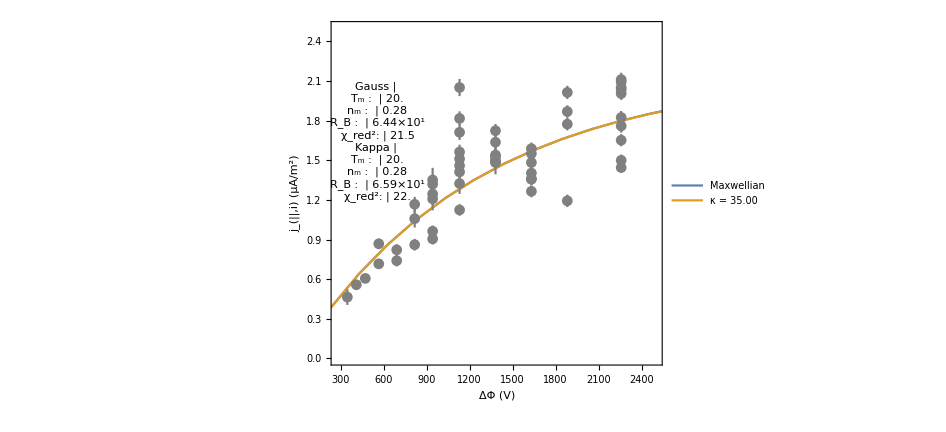

```mathematica
JVPlot=Show[Plot[{kFit[pot],gFit[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,23],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jErrData,PlotStyle->Gray]]
```

### J_E-V plot

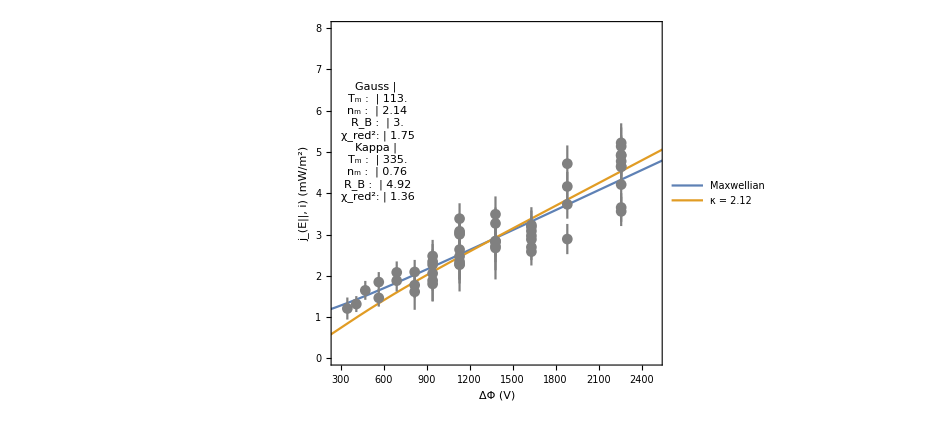

```mathematica
JeVPlot=Show[Plot[{kFitJeV[pot],gFitJeV[pot]},{pot,20,4000},PlotRange->{{minPot,maxPot},{0.,8}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestJeVKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",Style[StringForm["J_E-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,23],Epilog->Inset[JeVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jeErrData,PlotStyle->Gray]]
```

### Plots from combined fit

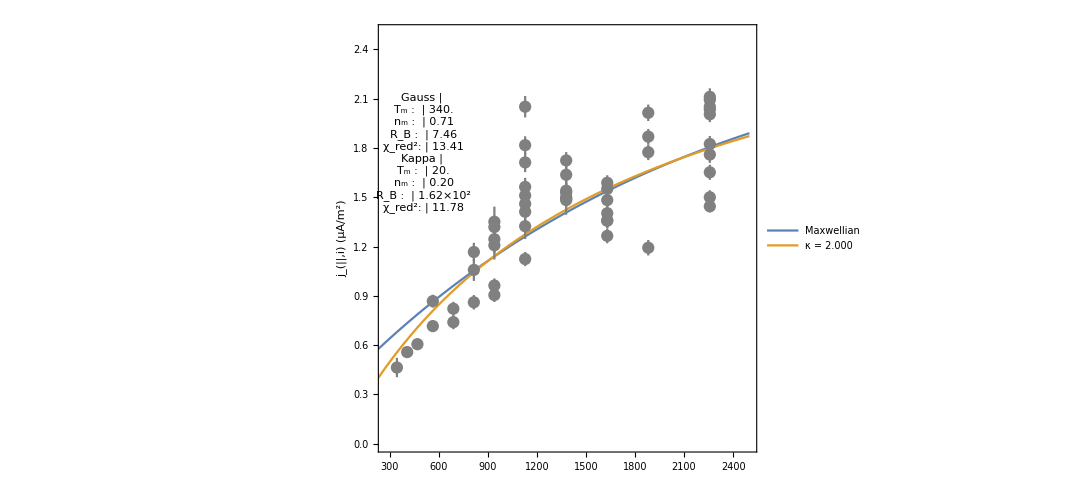
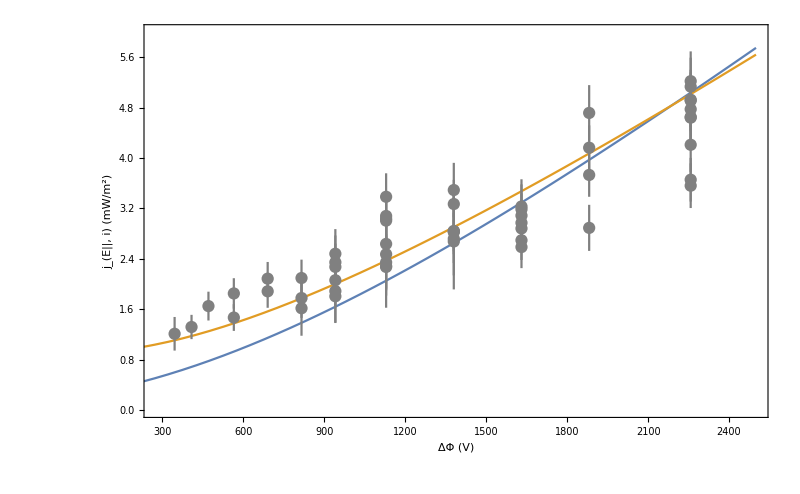

```mathematica
combPlot=Column[{combJVPlot,combJeVPlot}]
```

```mathematica
makePlots=1;
```

```mathematica
(*If[makePlots==1,Print["Making plots in "<>dir<>" ..."];Export[dir<>JVFilename,JVPlot];Export[dir<>JeVFilename,JeVPlot];Export[dir<>combJVFilename,combJVPlot];Export[dir<>combJeVFilename,combJeVPlot];Print["Done!"]]*)
```

```mathematica
If[makePlots==1,Print["Making plots in "<>dir<>" ..."];Export[dir<>JVFilename,JVPlot];Print[JeVFilename<>" ..."];Export[dir<>JeVFilename,JeVPlot];Print[combFilename<>" ..."];Export[dir<>combFilename,combPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/20180316/ ...

Orb1607__JeVFit__inds_65-97.png ...

Orb1607__combJVJeVFit__inds_65-97.png ...

Done!

Param tables

### J-V params

```mathematica
kFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.0788489 | 18.0635 | 0.0043651 | 0.996563
kFitT | 20.0084 | 211292. | 0.0000946954 | 0.999925
kFitRB | 999996. | 413.953 | 2415.72 | 1.33998×10^-53
kFitKappa | 1.5077 | 82.2571 | 0.0183292 | 0.985567

```mathematica
gFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.737783 | 2.50754 | 0.294226 | 0.771617
gFitT | 20. | 189.449 | 0.10557 | 0.916976
gFitRB | 336621. | 1.19817×10^10 | 0.0000280946 | 0.999978

### J_E-V params

```mathematica
kFitJeV["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.590468 | 12.8417 | 0.0459806 | 0.963806
kFitT | 20.0001 | 209.717 | 0.0953669 | 0.925022
kFitRB | 239189. | 4.5854×10^9 | 0.0000521631 | 0.999959
kFitKappa | 2.43713 | 84.7723 | 0.0287491 | 0.977365

```mathematica
gFitJeV["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.762078 | 0.387809 | 1.96508 | 0.063448
gFitT | 20. | 47.5033 | 0.421023 | 0.678228
gFitRB | 330538. | 6.09865×10^9 | 0.0000541986 | 0.999957

### Params from combined fit

```mathematica
kCombFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitRB | 805633. | 8.95543×10^9 | 0.0000899603 | 0.999929
kFitT | 20. | 157.058 | 0.127342 | 0.899278
kFitN | 0.491447 | 1.8178 | 0.270352 | 0.788213
kFitKappa | 2.0396 | 0.791263 | 2.57765 | 0.0135471

```mathematica
gCombFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitRB | 450860. | 4.64319×10^9 | 0.0000971014 | 0.999923
gFitT | 20. | 30.7434 | 0.650545 | 0.518801
gFitN | 0.738934 | 0.408339 | 1.80961 | 0.0773503

Mess ‘round, fit by eye

```mathematica
RBinit=gCombRB;Tminit=gCombT;nminit=gCombN;kappainit=kCombKappa;
```

```mathematica
Manipulate[Row[{Manipulate[Show[Plot[{JVMaxwellian[pot,RB,Tm,nm],JVKappa[pot,RB,Tm,nm,kappa]},{pot,100,1000},PlotRange->{{100,600},{0.,3}},PlotLegends->{"Maxwellian",StringForm["κ = `1`",NumberForm[kappa,{3,1}]]},FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->500,FrameStyle->(FontSize->18)],ErrorListPlot[jErrData]],{{RB,RBinit},1.01,100000},{{kappa,kappainit},1.501,35}],Manipulate[Show[Plot[{JEVMaxwellian[pot,RB,Tm,nm],JEVKappa[pot,RB,Tm,nm,kappa]},{pot,100,600},PlotRange->{Full,{0.,1.5}},PlotLegends->{"Maxwellian",StringForm["κ = `1`",NumberForm[kappa,{3,1}]]},FrameLabel->{"ΔΦ (V)","j_(E par, i) (mW/m^2)"},ImageSize->500,FrameStyle->(FontSize->18)],ErrorListPlot[jeErrData]],{{RB,RBinit},1.01,100000},{{kappa,kappainit},1.501,35}]}],{{Tm,Tminit},3,500},{{nm,nminit},0.1,5}]
```

Linear model, if we ever cared

## Linear model??

```mathematica
lm=LinearModelFit[plotData2,x,x,Weights->plotDataWts2]
```

FittedModel[0.571783+0.000828171 x]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.571783 | 0.209522 | 2.72899 | 0.0155285
x | 0.000828171 | 0.000104376 | 7.93453 | 9.52667×10^-7

```mathematica
Kmeas=(lm["BestFitParameters"])[[2]]
```

0.000828171

```mathematica
lm["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
lm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | 0.571783 | 0.209522 | {0.125197,1.01837}
x | 0.000828171 | 0.000104376 | {0.000605699,0.00105064}

```mathematica
lm["AdjustedRSquared"]
```

0.794758

#### See it

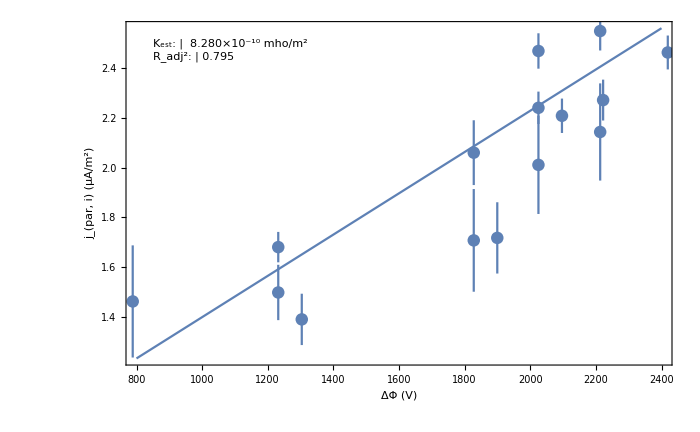

```mathematica
Show[Plot[lm[x],{x,800,2400},Frame->True,FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->700,FrameStyle->(FontSize->18),Epilog->Inset[TextGrid[Map[(Style[#,18])&,{{StringForm["K_est:"],StringForm[" `1` mho/m^2",NumberForm[Kmeas*1*^-6,{3,3},ScientificNotationThreshold->{-2,2}]]},{StringForm["R_adj^2:"],NumberForm[lm["AdjustedRSquared"],{3,3}]}},{2}]],Scaled[{0.05,0.95}],{-1,1}]],ErrorListPlot[errorData2]]
```

### Assess it

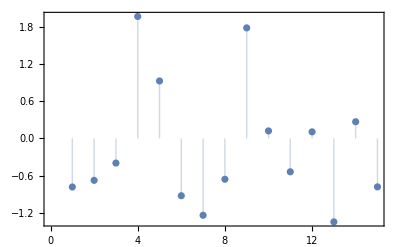

```mathematica
ListPlot[lm["StandardizedResiduals"],Frame->True,Filling->Axis]
```

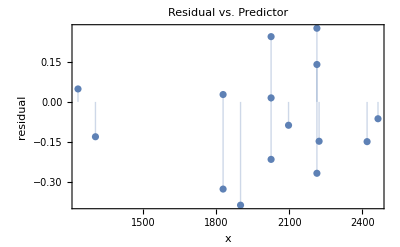

```mathematica
ListPlot[Transpose[{pots[[inds2]],lm["FitResiduals"]}],Frame->True,Filling->0,FrameLabel->{"x","residual"},PlotLabel->"Residual vs. Predictor"]
```

## Linear model for second half of arc

```mathematica
lm=LinearModelFit[plotData2,x,x,Weights->plotDataWts2]
```

FittedModel[0.571783+0.000828171 x]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.571783 | 0.209522 | 2.72899 | 0.0155285
x | 0.000828171 | 0.000104376 | 7.93453 | 9.52667×10^-7

```mathematica
Kmeas=(lm["BestFitParameters"])[[2]]
```

0.000828171

```mathematica
lm["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
lm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | 0.571783 | 0.209522 | {0.125197,1.01837}
x | 0.000828171 | 0.000104376 | {0.000605699,0.00105064}

```mathematica
lm["AdjustedRSquared"]
```

0.794758

#### See it

```mathematica
Show[Plot[lm[x],{x,800,2400},Frame->True,FrameLabel->{"ΔΦ (V)","j_(par, i) (μA/m^2)"},ImageSize->700,FrameStyle->(FontSize->18),Epilog->Inset[TextGrid[Map[(Style[#,18])&,{{StringForm["K_est:"],StringForm[" `1` mho/m^2",NumberForm[Kmeas*1*^-6,{3,3},ScientificNotationThreshold->{-2,2}]]},{StringForm["R_adj^2:"],NumberForm[lm["AdjustedRSquared"],{3,3}]}},{2}]],Scaled[{0.05,0.95}],{-1,1}]],ErrorListPlot[errorData2]]
```

-Graphics-

### Assess it

```mathematica
ListPlot[lm["StandardizedResiduals"],Frame->True,Filling->Axis]
```

-Graphics-

```mathematica
ListPlot[Transpose[{pots[[inds2]],lm["FitResiduals"]}],Frame->True,Filling->0,FrameLabel->{"x","residual"},PlotLabel->"Residual vs. Predictor"]
```

-Graphics-